```mathematica
Psi[x_,n_]=1/Sqrt[xf] Sin[n π (x+xf)/(2xf)];
```

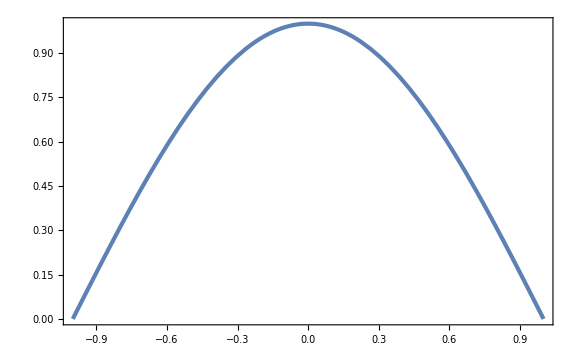

```mathematica
Plot[Psi[x,1]/.{xf->1},{x,-1,1}]
```

```mathematica
Simplify[Integrate[Psi[x,n]Psi[x,n],{x,-xf,xf}],{n∈Integers}]
```

1

```mathematica
Simplify[Integrate[Psi[x,n]Psi[x,m],{x,-xf,xf}],{n∈Integers,m∈Integers}]
```

0

```mathematica
normN=Integrate[E^(-x^2/(2 r^2 xf^2)2),{x,-xf,xf}]
```

√π r xf Erf[1/r]

```mathematica
ft1[x_,r_]=1/Sqrt[normN] E^(-x^2/(2 r^2 xf^2))
```

(ⅇ^(-x^2/(2 r^2 xf^2)))/(π^(1/4) √(r xf Erf[1/r]))

```mathematica
Integrate[ft1[x,r]^2,{x,-xf,xf}]
```

1

```mathematica
FullSimplify[Integrate[Psi[x,2m+1]ft1[x,r],{x,-xf,xf}],{xf>0,r>0,m∈Integers}]/.{m->(n-1)/2}//Simplify
```

(ⅇ^(-1/8 π (-4 ⅈ+4 ⅈ n+n^2 π r^2)) π^(1/4) r (Erf[(2-ⅈ n π r^2)/(2 √2 r)]+Erf[(2+ⅈ n π r^2)/(2 √2 r)]))/(√2 √(r Erf[1/r]))

```mathematica
Overwrap[r_,n_]:=NIntegrate[Psi[x,n]ft1[x,r]/.{xf->1},{x,-1,1}]
```

```mathematica
Overwrap1[r_]=FullSimplify[Integrate[Psi[x,1]ft1[x,r],{x,-xf,xf}],{xf>0,r>0}]
```

(ⅇ^(-1/8 π^2 r^2) π^(1/4) r (Erf[(2-ⅈ π r^2)/(2 √2 r)]+Erf[(2+ⅈ π r^2)/(2 √2 r)]))/(√2 √(r Erf[1/r]))

```mathematica
FindMaximum[{Overwrap1[r]^2,r>0},r]
```

{0.994638,{r→0.519941}}

```mathematica
rmax=r/.FindMaximum[{Overwrap1[r]^2,r>0},r][[2]]
```

0.519941

```mathematica
pad={{100,10},{70,50}};
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

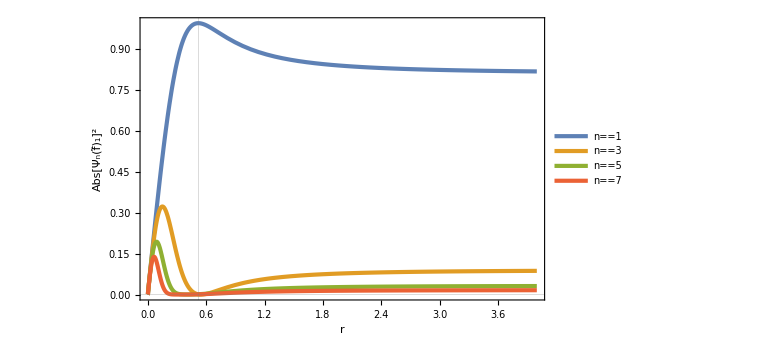

```mathematica
Plot[{Overwrap[r,1]^2,Overwrap[r,3]^2,Overwrap[r,5]^2,Overwrap[r,7]^2},{r,0,4},GridLines->{{rmax},{0}},FrameLabel->{r,Abs[BraKet[{Subscript[Ψ, n]},{Subscript[OverTilde[f], 1]}]]^2},PlotLegends->Placed[{n==1,n==3,n==5,n==7},{0.8,0.45}],ImagePadding->pad]
```

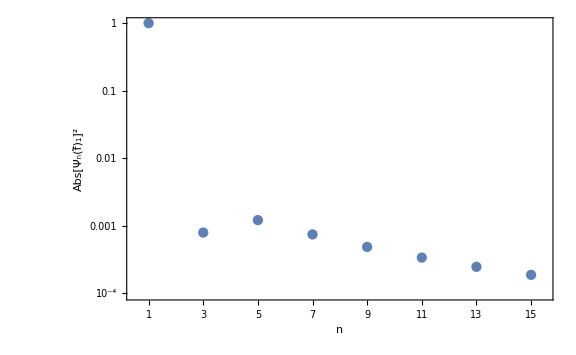

```mathematica
ListLogPlot[Table[{n,Overwrap[rmax,n]^2},{n,1,15,2}],Joined->False,PlotRange->{{0.5,15.5},Full},FrameTicks->{Automatic,{Join[Table[n,{n,1,15,2}],Table[{n,""},{n,2,14,2}]],Table[{n,""},{n,1,15}]}},FrameLabel->{{Abs[BraKet[{Subscript[Ψ, n]},{Subscript[OverTilde[f], 1]}]]^2,None},{n,r==Subscript[r, max]}},ImagePadding->pad]
```